```mathematica
mesh = Import["/home/biokitten/Builds/hello_deal.ii/step4/solution-2d.vtk"]
```

-Graphics3D-

```mathematica
elements=Import["/home/biokitten/Builds/hello_deal.ii/step4/solution-2d.vtk","Elements"]
```

{CuboidData,CuboidObjects,Graphics3D,GraphicsComplex,LineData,LineObjects,PointData,PointObjects,PolygonData,PolygonObjects,VertexData}

```mathematica
listOdata=Table[
Import["/home/biokitten/Builds/hello_deal.ii/step4/solution-2d.vtk",elem],
{elem,elements}]
```

{{},{},7,{1},{{-1,-1,0},{-0.875,-1,0},{-1,-0.875,0},{-0.875,-0.875,0},{-0.875,-1,0},{-0.75,-1,0},{-0.875,-0.875,0},{-0.75,-0.875,0},{-1,-0.875,0},{-0.875,-0.875,0},1004,{0.875,0.875,0},{1,0.875,0},{0.75,0.875,0},{0.875,0.875,0},{0.75,1,0},{0.875,1,0},{0.875,0.875,0},{1,0.875,0},{0.875,1,0},{1,1,0}}}
 |  |  |  |

```mathematica
stream=OpenRead["/home/biokitten/Builds/hello_deal.ii/step4/solution-2d.vtk"];
```

```mathematica
match="POINT_DATA";
word=Read[stream,Word];
While[word≠match,
word=Read[stream,Word];
]
```

```mathematica
numPoints=Read[stream,Number]
```

1024

```mathematica
Read[stream,Record]
```

LOOKUP_TABLE default

```mathematica
pointData=ReadList[stream,Number,numPoints];
```

```mathematica
Close[stream]
```

/home/biokitten/Builds/hello_deal.ii/step4/solution-2d.vtk

```mathematica
getVTKPointData[filename_]:=Module[
{stream,match,word,numPoints},
stream=OpenRead[filename];
match="POINT_DATA";
word=Read[stream,Word];
While[word≠match,
word=Read[stream,Word];
];
numPoints=Read[stream,Number];
Skip[stream,Record,2];
pointData=ReadList[stream,Number,numPoints];
Close[stream];
pointData
]
```

```mathematica
data=getVTKPointData["/home/biokitten/Builds/hello_deal.ii/step4/solution-2d.vtk"];
```

```mathematica
Short[pointData]
```

{2,1.76562,1.76562,1.69423,1.76562,1.5625,«1013»,1.76562,1.69423,1.76562,1.76562,2}

```mathematica
replacez[{x_,y_,z_},znew_]={x,y,znew}
```

{x,y,znew}

```mathematica
threeDPoints=MapThread[replacez,{listOdata[[-1]],pointData}];
```

```mathematica
twoDPoints=Map[truncate,listOdata[[-1]]];
```

```mathematica
ListPlot3D[threeDPoints,PlotRange->All]
```

-Graphics3D-

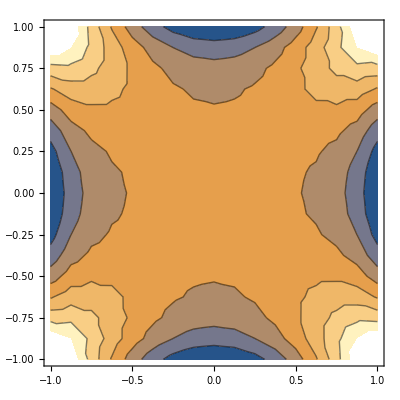

```mathematica
ListContourPlot[threeDPoints]
```